# The Classical Zeeman Effect

In this experiment, we investigate the classical theory of Zeeman splitting, i.e. the splitting of spectral lines in the presence of a magnetic field. We find spectral lines that, after a preliminary verification described in the lab procedure (identifying the 585.2 nm spectral line by its position and brightness, then varying the magnetic field and finding the unique line that matches the Δm of the first line - we use Δm = 1 and Δm = 2 as point checks - to find the 626.6 nm line) appear to be adequately described by the classical Zeeman-Lorentz theory. We call these lines Normal Zeeman line, and we are given that the spectral lines for 585.3 nm and 626.6 nm are Normal Zeeman).

Observing the fringes on the line for 626.6 nm, we vary the magnetic field to obtain identifiable Δm settings, and measure the magnetic field at every such setting to obtain our (Δm, B) data set, which we fit against a linear model to verify the linear relation between Δm and B determined in the prelab for Normal Zeeman lines. We can then use the fit parameters to obtain an estimate for e/m.

Analysis in CurveFit

```mathematica
<<CurveFit`
```

CurveFit for Mathematica v7.x thru v10.x, Version 1.95, 1/2016

Caltech Sophomore Physics Labs, Pasadena, CA

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph6/Lab 7/zeeman.dat

LoadFile::sorted: Data sorted in increasing x order.

Read 38 data points.

```mathematica
(* We multiply by 10^-4 to convert the B-field data from Gauss to Tesla. *)
```

```mathematica
xnew[ x_, y_ ] := x 
ynew[ x_, y_ ] := 10^-4 y 

DataTransform[]

(* Use Undo[] if you don't like the results. *)
```

All 38 points transformed.

```mathematica
(* We use CurveFit to analyze the dataset and assign uncertainties in our B values. *)
```

```mathematica
CalculateYsigmas[]
```

Sorted data in order of increasing X values.

Calculated and assigned Y uncertainties.

```mathematica
LinearFit[]
```

n = 38

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-0.00797991 | b= 
0.827603 | 
σ_a= 
0.00589609 | σ_b= 
0.0048984 | Std. deviation= 
0.0161128

Fit of (x,y±σ_y)

a= 
0.000913702 | b= 
0.82366 | 
σ_a= 
0.00226904 | σ_b= 
0.00183055 | χ^2/(n-2)= 
2.43896

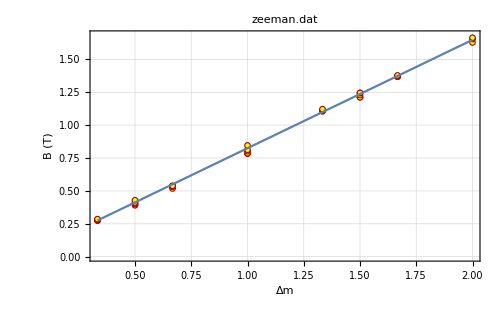
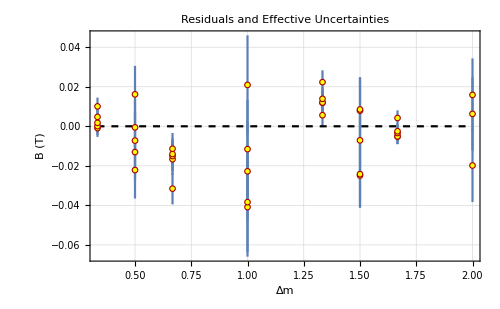
-Graphics-
-Graphics-
y(x) = a + b x
a= 
0.000913702 | b= 
0.82366 | 
σ_a= 
0.00226904 | σ_b= 
0.00183055 | χ^2/(n-2)= 
2.43896

```mathematica
LinearDifferencePlot[FrameLabel->{"Δm","B (T)"}]
```

Comments on the fit

We know from problem 5 of the prelab that for Normal Zeeman lines, Δm and B are related by |Δm| = de/(2π c m)B, i.e. we expect Δm and B to be directly proportional. We therefore perform a linear fit, as this allows us to perform a fit of the slope while disregarding systematic uncertainties that result in an offset.

In this case, if systematic uncertainties of this type have been successfully avoided (for instance, if the Hall probe has been zeroed correctly), we expect our y-intercept to be consistent with 0. This allows us to detect some systematic uncertainties, that show up as a non-zero intercept. In this case, we obtain a y-intercept a = 0.001 ± 0.002 T, which is consistent with zero. This indicates that we have been reasonably successful in avoiding systematic errors in the course of the experiment. (Note that there could still be sources of systematic errors not indicated by the y-intercept - for example, calibration of the Hall probe).

Our fit has a reasonably small (χ̃)^2=2.44, indicating that the data is reasonably free of statistical errors and that our linear model fits the data well. Along with our y-intercept being consistent with 0, this tends to support Lorentz’s theoretical predictions for the normal Zeeman spectral line. We can obtain further confirmation by using our fit parameter b to obtain an estimate for e/m and comparing it to accepted experimental estimates of e/m.

Estimating e/m

We use the fit parameter b to obtain an estimate for e/m as per the proportionality relation described above: b=d/(2π c)e/m ⇒ e/m=(2π c b)/d.

We have the following measurements for d: 0.0132 m, 0.0132 m, 0.01315 m, 0.01315 m. Then,

```mathematica
dValues={0.0132,0.0132,0.01315,0.01315};
d={Mean[dValues],StandardDeviation[dValues]/Sqrt[Length[dValues]]}
```

{0.013175,0.0000144338}

we have d = 0.01318 ± 0.00001 m. From this, we obtain

```mathematica
c=299792458;
emRatio=2π c 0.82366/d[[1]]{1,Sqrt[(d[[2]]/d[[1]])^2+(0.00183055/0.82366)^2]}
```

{1.1776×10^11,2.91787×10^8}

e/m = (1.178 ± 0.003) × 10^11 C kg^-1. We compare this to the NIST value of e/m = 1.7588 × 10^11 C kg^-1 and observe that while our e/m is of the right magnitude, it significantly underestimates the accepted experimental value for e/m (we are more than 5σ off).

Final comments

Given the results above and the small statistical error in our estimate, the significant underestimate of e/m suggests a significant source of systematic error in our experiment. We propose that a major source of systematic error lies in the method of generation of the B-field. We are generating the B-field using large electromagnets and a constant voltage power supply. However, the magnetic field generated by an electromagnet depends on the current through the coils, and not directly on the voltage across it. This could constitute a source of error at high voltages, as large currents flow through the coil, heating the wires via ohmic losses, causing the resistance to increase, and the current and therefore the magnetic field to decrease with time (at constant voltage a smaller current will flow through a higher resistance coil). This could cause our B-field values to decrease between the moment we set our Δm and insert the Hall probe to measure the B-field, causing our measurements of B and therefore our estimate of b (the fit parameter) to be significant underestimates. This is consistent with the value we have obtained for e/m. One possible solution is to use a constant-current power supply instead and redo the experiment.

There is another feature of the classical Lorentz model that we can test: the model predicts that given our configuration, a linearly polarized filter should either allow the un-split fringe (corresponding to linear motion along B-field axis) to pass through or the satellite fringes, depending on the filter’s orientation. By adjusting our Δm settings (via changing the B-field) and switching back and forth between orientations of the filter, this is exactly what we observe for Normal Zeeman lines, confirming that polarization of these fringes is adequately described by the classical Lorentz model. However we also observe that this is not true for all spectral lines, indicating that the polarizations of spectral lines are in general inadequately described by the classical Lorentz model.